```mathematica
SetDirectory[NotebookDirectory[]]
height=0.5;
ks=2*Pi/(1);
hs=height-0.05;
M2=5;
g=980;
σ=72;
ρ=1;

A1d[q_,ks_,As_]:=Module[{κ},κ[k_, n_]:=k+n*ks;-Table[(1/2-Tanh[Norm[κ[q,n1]]*height]/2)*(g+σ/ρ*Norm[κ[q,n1]]^2)*Norm[κ[q,n1]]*(BesselI[n1-n2,Norm[κ[q,n1]]*As]+1/2*ks*As*(κ[q,n1]/Norm[κ[q,n1]]*(BesselI[n1-n2+1,Norm[κ[q,n1]]*As]-BesselI[n1-n2-1,Norm[κ[q,n1]]*As])))-(1/2+Tanh[Norm[κ[q,n1]]*height]/2)*(g+σ/ρ*Norm[κ[q,n1]]^2)*Norm[κ[q,n1]]*(BesselI[n1-n2,-Norm[κ[q,n1]]*As]+1/2*ks*As*(κ[q,n1]/Norm[κ[q,n1]]*(BesselI[n1-n2+1,-Norm[κ[q,n1]]*As]-BesselI[n1-n2-1,-Norm[κ[q,n1]]*As]))),{n1,-M2,M2},{n2,-M2,M2}]]

B1d[q_,ks_,As_]:=Module[{κ},κ[k_, n_]:=k+n*ks;-Table[(1/2-Tanh[Norm[κ[q,n1]]*height]/2)*(BesselI[n1-n2,Norm[κ[q,n1]]*As]+1/2*ks*As*(κ[q,n1]/Norm[κ[q,n1]]*(BesselI[n1-n2+1,Norm[κ[q,n1]]*As]-BesselI[n1-n2-1,Norm[κ[q,n1]]*As])))+(1/2+Tanh[Norm[κ[q,n1]]*height]/2)*(BesselI[n1-n2,-Norm[κ[q,n1]]*As]+1/2*ks*As*(κ[q,n1]/Norm[κ[q,n1]]*(BesselI[n1-n2+1,-Norm[κ[q,n1]]*As]-BesselI[n1-n2-1,-Norm[κ[q,n1]]*As]))),{n1,-M2,M2},{n2,-M2,M2}]]


A2d[q_,ks_,As_,k1_,k2_]:=Module[{κ},κ[k_, n_,m_]:=k+n*ks*k1+m*ks*k2;ArrayFlatten[-Table[(1/2-Tanh[Norm[κ[q,n1,m1]]*height]/2)*(g+σ/ρ*Norm[κ[q,n1,m1]]^2)*Norm[κ[q,n1,m1]]*(BesselI[n1-n2,Norm[κ[q,n1,m1]]*As/2]*BesselI[m1-m2,Norm[κ[q,n1,m1]]*As/2]+1/4*ks*As*(κ[q,n1,m1].k1/Norm[κ[q,n1,m1]]*(BesselI[n1-n2+1,Norm[κ[q,n1,m1]]*As/2]-BesselI[n1-n2-1,Norm[κ[q,n1,m1]]*As/2])*BesselI[m1-m2,Norm[κ[q,n1,m1]]*As/2]+κ[q,n1,m1].k2/Norm[κ[q,n1,m1]]*BesselI[n1-n2,Norm[κ[q,n1,m1]]*As/2]*(BesselI[m1-m2+1,Norm[κ[q,n1,m1]]*As/2]-BesselI[m1-m2-1,Norm[κ[q,n1,m1]]*As/2])))-(1/2+Tanh[Norm[κ[q,n1,m1]]*height]/2)*(g+σ/ρ*Norm[κ[q,n1,m1]]^2)*Norm[κ[q,n1,m1]]*(BesselI[n1-n2,-Norm[κ[q,n1,m1]]*As/2]*BesselI[m1-m2,-Norm[κ[q,n1,m1]]*As/2]+1/4*ks*As*(κ[q,n1,m1].k1/Norm[κ[q,n1,m1]]*(BesselI[n1-n2+1,-Norm[κ[q,n1,m1]]*As/2]-BesselI[n1-n2-1,-Norm[κ[q,n1,m1]]*As/2])*BesselI[m1-m2,-Norm[κ[q,n1,m1]]*As/2]+κ[q,n1,m1].k2/Norm[κ[q,n1,m1]]*BesselI[n1-n2,-Norm[κ[q,n1,m1]]*As/2]*(BesselI[m1-m2+1,-Norm[κ[q,n1,m1]]*As/2]-BesselI[m1-m2-1,-Norm[κ[q,n1,m1]]*As/2]))),{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]]]

B2d[q_,ks_,As_,k1_,k2_]:=Module[{κ},κ[k_, n_,m_]:=q+n*ks*k1+m*ks*k2;ArrayFlatten[-Table[(1/2-Tanh[Norm[κ[q,n1,m1]]*height]/2)*(BesselI[n1-n2,Norm[κ[q,n1,m1]]*As/2]*BesselI[m1-m2,Norm[κ[q,n1,m1]]*As/2]+1/4*ks*As*(κ[q,n1,m1].k1/Norm[κ[q,n1,m1]]*(BesselI[n1-n2+1,Norm[κ[q,n1,m1]]*As/2]-BesselI[n1-n2-1,Norm[κ[q,n1,m1]]*As/2])*BesselI[m1-m2,Norm[κ[q,n1,m1]]*As/2]+κ[q,n1,m1].k2/Norm[κ[q,n1,m1]]*BesselI[n1-n2,Norm[κ[q,n1,m1]]*As/2]*(BesselI[m1-m2+1,Norm[κ[q,n1,m1]]*As/2]-BesselI[m1-m2-1,Norm[κ[q,n1,m1]]*As/2])))+(1/2+Tanh[Norm[κ[q,n1,m1]]*height]/2)*(BesselI[n1-n2,-Norm[κ[q,n1,m1]]*As/2]*BesselI[m1-m2,-Norm[κ[q,n1,m1]]*As/2]+1/4*ks*As*(κ[q,n1,m1].k1/Norm[κ[q,n1,m1]]*(BesselI[n1-n2+1,-Norm[κ[q,n1,m1]]*As/2]-BesselI[n1-n2-1,-Norm[κ[q,n1,m1]]*As/2])*BesselI[m1-m2,-Norm[κ[q,n1,m1]]*As/2]+κ[q,n1,m1].k2/Norm[κ[q,n1,m1]]*BesselI[n1-n2,-Norm[κ[q,n1,m1]]*As/2]*(BesselI[m1-m2+1,-Norm[κ[q,n1,m1]]*As/2]-BesselI[m1-m2-1,-Norm[κ[q,n1,m1]]*As/2]))),{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]]]
```

/Users/zack/Desktop/shaker_docs/faraday

## One dimensional sinusoidal heterogeneity

```mathematica
num=100;
sys1d[q_,A_]:={A1d[q,ks,A],B1d[q,ks,A]}
AbsoluteTiming[vals11d=Table[#^(1/2)/(2*Pi)&/@SingularValueList[sys1d[t*ks/2,hs]],{t,0.01,2-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals21d=Table[#^(1/2)/(2*Pi)&/@SingularValueList[sys1d[t*ks/2,0.001]],{t,0.01,2-0.01,(1-0.01)/num}];]
```

{6.65246,Null}

{5.43791,Null}

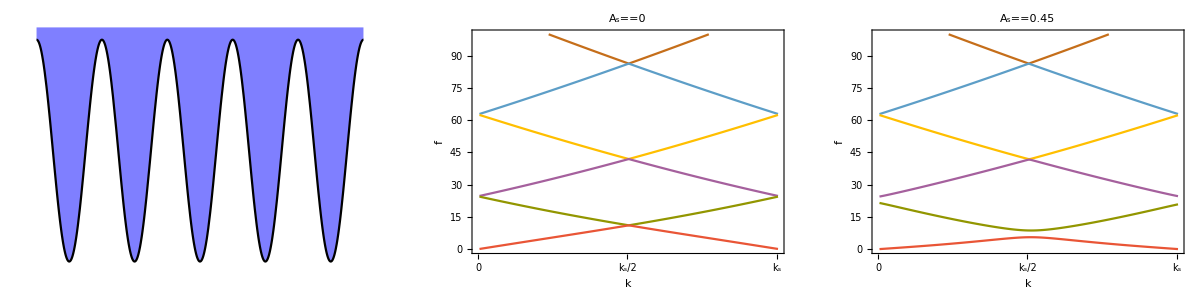

```mathematica
p=Grid[{{Plot[hs*Cos[ks*x],{x,0,2*Pi*5/ks},PlotStyle->Black,PlotRange->{-1.1*hs,height},Axes->False,Filling->Top,FillingStyle->Directive[Opacity[0.5],Blue],ImageSize->300],ListPlot[Transpose[vals21d],Joined->True,PlotRange->{0,100},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,Subscript[k,s]/2},{2*num,Subscript[k,s]}},{{0,""},{num,""},{2*num,""}}}},ImageSize->300,PlotLabel->Subscript[A,s]==0,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],
ListPlot[Transpose[vals11d],Joined->True,PlotRange->{0,100},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,Subscript[k,s]/2},{2*num,Subscript[k,s]}},{{0,""},{num,""},{2*num,""}}}},ImageSize->300,PlotLabel->Subscript[A,s]==hs,AspectRatio->1,ImagePadding->{{65,15},{65,15}}]}}]
```

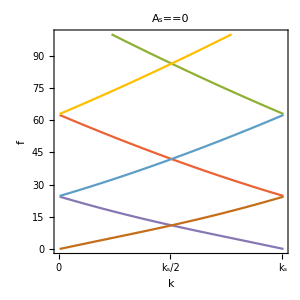

```mathematica
ListPlot[Transpose[Table[#^(1/2)/(2*Pi)&/@Table[(g+σ/ρ*(n*ks+t*ks/2)^2)*(n*ks+t*ks/2)*Tanh[(n*ks+t*ks/2)*height],{n,-5,5}],{t,0.01,2-0.01,(1-0.01)/num}]],Joined->True,PlotRange->{0,100},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,Subscript[k,s]/2},{2*num,Subscript[k,s]}},{{0,""},{num,""},{2*num,""}}}},ImageSize->300,PlotLabel->Subscript[A,s]==0,AspectRatio->1,ImagePadding->{{65,15},{65,15}}]
```

```mathematica
Export["1d.pdf",p]
```

1d.pdf

#### Convergence

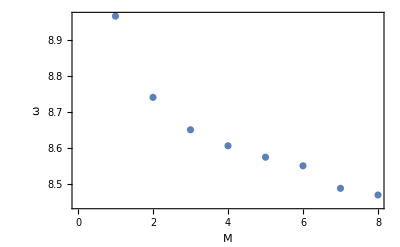

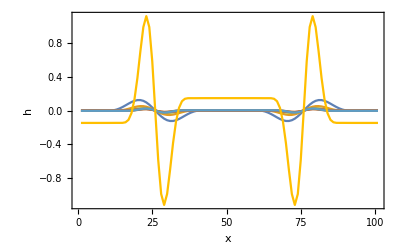

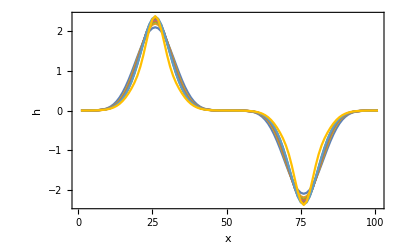

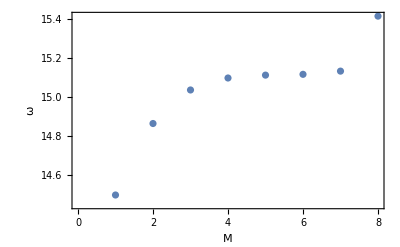

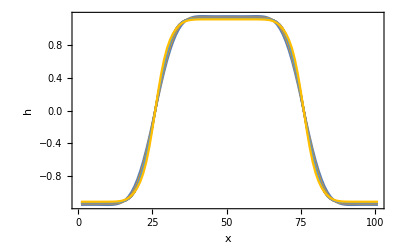

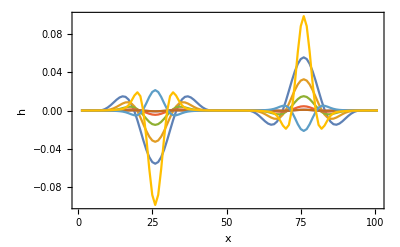

```mathematica
test=Table[Eigensystem[sysflat[ks/2,hs]],{M2,3,10}];

ListPlot[(-test[[All,1,-1]])^(1/2)/(2*Pi),Axes->False,Frame->True,FrameLabel->{M,ω},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
test2=Table[Table[Total[test[[M2-2,2,-1]]*Sign[test[[M2-2,2,-1,M2]]]*Table[Exp[I*(κ[ks/2,n])*x],{n,-M2,M2}]],{x,-Pi/(ks/2),Pi/(ks/2),2*Pi/(ks/2)/100}],{M2,3,10}];
ListPlot[Re[test2],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{x,h},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
ListPlot[Im[test2],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{x,h},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]

ListPlot[(-test[[All,1,-2]])^(1/2)/(2*Pi),Axes->False,Frame->True,FrameLabel->{M,ω},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
test2=Table[Table[Total[test[[M2-2,2,-2]]*Sign[test[[M2-2,2,-2,M2]]]*Table[Exp[I*(κ[ks/2,n])*x],{n,-M2,M2}]],{x,-Pi/(ks/2),Pi/(ks/2),2*Pi/(ks/2)/100}],{M2,3,10}];
ListPlot[Re[test2],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{x,h},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
ListPlot[Im[test2],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{x,h},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
```

## Square heterogeneity

```mathematica
r1={0,1};
r2={1,0};
k1={0,1};
k2={1,0};
```

```mathematica
num=25;
syssquare[q_,A_]:={A2d[q,ks,A,k1,k2],B2d[q,ks,A,k1,k2]};
AbsoluteTiming[vals1square=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,hs]],{t,0.01,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals2square=Table[q=ks*k1/2+t*ks*((k1+k2)/2-k1/2);#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,hs]],{t,0,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals3square=Table[q=ks*(k1+k2)/2*(1-t);#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,hs]],{t,0,1-0.01,(1-0.01)/num}];]

AbsoluteTiming[vals4square=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,0.01]],{t,0.01,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals5square=Table[q=ks*k1/2+t*ks*((k1+k2)/2-k1/2);#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,0.01]],{t,0,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals6square=Table[q=ks*(k1+k2)/2*(1-t);#^(1/2)/(2*Pi)&/@SingularValueList[syssquare[q,0.01]],{t,0,1-0.01,(1-0.01)/num}];]
```

{361.751,Null}

{377.106,Null}

{370.684,Null}

{338.927,Null}

{352.846,Null}

{352.731,Null}

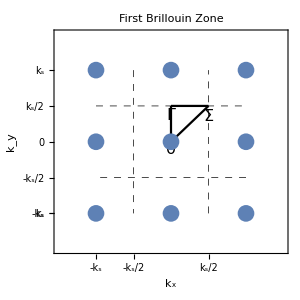
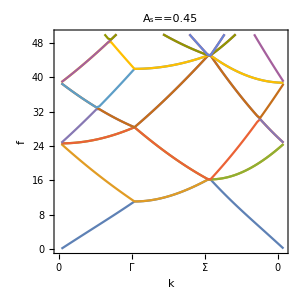
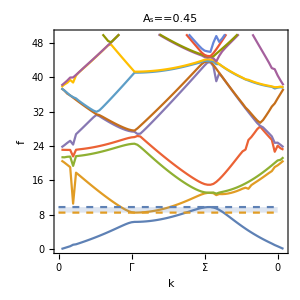
-Graphics3D- | -Graphics- | -Graphics- | -Graphics-

```mathematica
p=Grid[{{ListPlot3D[Flatten[Table[{x,y,1/2*(hs*Sin[ks*{x,y}.k1]+hs*Sin[ks*{x,y}.k2])},{x,0,2*Pi*5/ks,2*Pi*5/ks/100},{y,0,2*Pi*5/ks,2*Pi*5/ks/100}],1],PlotRange->{-hs,height},Boxed->False,Axes->False,Filling->Top,FillingStyle->Directive[Opacity[0.5],Blue],ImageSize->300],Show[ParametricPlot[{ks*(k2/2+t*k1),-ks*(k2/2+t*k1),ks*(k1/2+t*k2),-ks*(k1/2+t*k2)},{t,-1,1},PlotStyle->Directive[Black,Dashed,AbsoluteThickness[0.5]],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-3/2*ks,3/2*ks},{-3/2*ks,3/2*ks}},ImageSize->300,FrameTicks->{{{{-ks,Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}},{{{-ks,-Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}}},ImagePadding->{{65,15},{65,15}},PlotLabel->"First Brillouin Zone"],ParametricPlot[{t*ks*k1/2,ks*k1/2+t*ks*((k1+k2)/2-k1/2),ks*(k1+k2)/2*(1-t)},{t,0,1},PlotStyle->Directive[Black],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-ks,ks},{-ks,ks}},PlotLabels->Placed[{0,Γ,Σ},Scaled[0]]],ListPlot[Flatten[Table[ks*(n*k1+m*k2),{n,-M2,M2},{m,-M2,M2}],1],AspectRatio->1,PlotRange->{{-2,2},{-2,2}},Axes->False,Frame->True,PlotStyle->Directive[PointSize[0.04]]]],ListPlot[Reverse[Transpose[Join[vals4square,vals5square,vals6square]]],PlotLabel->Subscript[A,s]==hs,Joined->True,PlotRange->{0,50},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],
Show[ListPlot[Reverse[Transpose[Join[vals1square,vals2square,vals3square]]],PlotLabel->Subscript[A,s]==hs,Joined->True,PlotRange->{0,50},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],Plot[{Max[Transpose[Join[vals1square,vals2square,vals3square]][[-1,All]]],Min[Transpose[Join[vals1square,vals2square,vals3square]][[-2,All]]]},{x,0,3*num},Filling->True,PlotStyle->Dashed]]}}]
```

```mathematica
AbsoluteTiming[vals4flatsquare=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1],{t,0.01,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals5flatsquare=Table[q=ks*k1/2+t*ks*((k1+k2)/2-k1/2);#^(1/2)/(2*Pi)&/@Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1],{t,0,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals6flatsquare=Table[q=ks*(k1+k2)/2*(1-t);#^(1/2)/(2*Pi)&/@Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1],{t,0,1-0.01,(1-0.01)/num}];]
```

{0.110793,Null}

{0.118464,Null}

{0.119155,Null}

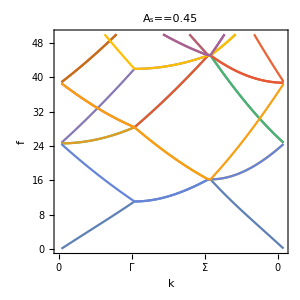

```mathematica
ListPlot[Reverse[Transpose[Join[vals4flatsquare,vals5flatsquare,vals6flatsquare]]],PlotLabel->Subscript[A,s]==hs,Joined->True,PlotRange->{0,50},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}]
```

```mathematica
Export["square.pdf",p]
```

square.pdf

## Hexagonal heterogeneity

```mathematica
r1={1,0};
r2={1/2,3^(1/2)/2};
k1={1,-1/3^(1/2)};
k2={0,2/3^(1/2)};
```

```mathematica
num=25;
syshex[q_,A_]:={A2d[q,ks,A,k1,k2],B2d[q,ks,A,k1,k2]};
AbsoluteTiming[vals1hex=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]],{t,0.01,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals2hex=Table[q=ks*k1/2+t*ks*((2*k1+k2)/3-k1/2);#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]],{t,0,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals3hex=Table[q=ks*(2*k1+k2)/3*(1-t);#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,hs]],{t,0,1-0.01,(1-0.01)/num}];]

AbsoluteTiming[vals4hex=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,0.01]],{t,0.01,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals5hex=Table[q=ks*k1/2+t*ks*((2*k1+k2)/3-k1/2);#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,0.01]],{t,0,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals6hex=Table[q=ks*(2*k1+k2)/3*(1-t);#^(1/2)/(2*Pi)&/@SingularValueList[syshex[q,0.01]],{t,0,1-0.01,(1-0.01)/num}];]
```

{586.818,Null}

{648.281,Null}

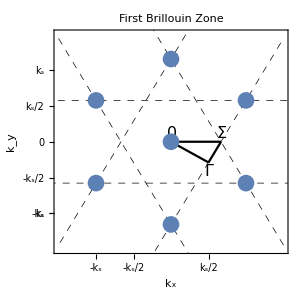
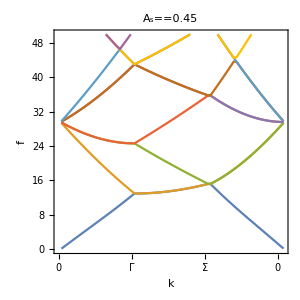
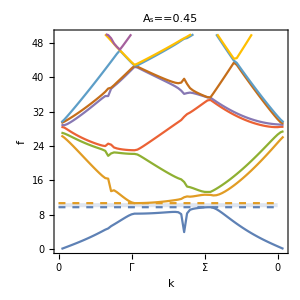
-Graphics3D- | -Graphics- | -Graphics- | -Graphics-

```mathematica
p=Grid[{{ListPlot3D[Flatten[Table[{x,y,1/2*(hs*Sin[ks*{x,y}.k1]+hs*Sin[ks*{x,y}.k2])},{x,0,2*Pi*5/ks,2*Pi*5/ks/100},{y,0,2*Pi*5/ks,2*Pi*5/ks/100}],1],PlotRange->{-hs,height},Boxed->False,Axes->False,Filling->Top,FillingStyle->Directive[Opacity[0.5],Blue],ImageSize->300],Show[ParametricPlot[{ks*(k1+t*(k2-k1)),ks*(k1+k2+t*(-k1-(k1+k2))),-ks*(k1+t*(k2-k1)),-ks*(k1+k2+t*(-k1-(k1+k2))),ks*(k2+t*(-k1-2*k2)),-ks*(k2+t*(-k1-2*k2))},{t,-0.5,1.5},PlotStyle->Directive[Black,Dashed,AbsoluteThickness[0.5]],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-3/2*ks,3/2*ks},{-3/2*ks,3/2*ks}},ImageSize->300,FrameTicks->{{{{-ks,Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}},{{{-ks,-Subscript[k,s]},{-ks,-Subscript[k,s]},{-ks/2,-Subscript[k,s]/2},{0,0},{ks/2,Subscript[k,s]/2},{ks,Subscript[k,s]}},{{-ks,""},{-ks,""},{-ks/2,""},{0,""},{ks/2,""},{ks,""}}}},ImagePadding->{{65,15},{65,15}},PlotLabel->"First Brillouin Zone"],ParametricPlot[{t*ks*k1/2,ks*k1/2+t*ks*((2*k1+k2)/3-k1/2),ks*(2*k1+k2)/3*(1-t)},{t,0,1},PlotStyle->Directive[Black],Axes->False,Frame->True,FrameLabel->{Subscript[k,x],Subscript[k,y]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotRange->{{-ks,ks},{-ks,ks}},PlotLabels->Placed[{0,Γ,Σ},Scaled[0]]],ListPlot[Flatten[Table[ks*(n*k1+m*k2),{n,-M2,M2},{m,-M2,M2}],1],AspectRatio->1,PlotRange->{{-2,2},{-2,2}},Axes->False,Frame->True,PlotStyle->Directive[PointSize[0.04]]]],ListPlot[Reverse[Transpose[Join[vals4hex,vals5hex,vals6hex]]],PlotLabel->Subscript[A,s]==hs,Joined->True,PlotRange->{0,50},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],
Show[ListPlot[Reverse[Transpose[Join[vals1hex,vals2hex,vals3hex]]],PlotLabel->Subscript[A,s]==hs,Joined->True,PlotRange->{0,50},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}],Plot[{Max[Transpose[Join[vals1hex,vals2hex,vals3hex]][[-1,All]]],Min[Transpose[Join[vals1hex,vals2hex,vals3hex]][[-2,All]]]},{x,0,3*num},Filling->True,PlotStyle->Dashed]]}}]
```

```mathematica
Export["hexagonal.pdf",p]
```

hexagonal.pdf

```mathematica
AbsoluteTiming[vals4flathex=Table[q=t*ks*k1/2;#^(1/2)/(2*Pi)&/@Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1],{t,0.01,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals5flathex=Table[q=ks*k1/2+t*ks*((2*k1+k2)/3-k1/2);#^(1/2)/(2*Pi)&/@Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1],{t,0,1-0.01,(1-0.01)/num}];]
AbsoluteTiming[vals6flathex=Table[q=ks*(2*k1+k2)/3*(1-t);#^(1/2)/(2*Pi)&/@Flatten[Table[(g+σ/ρ*(Norm[n*ks*k1+m*ks*k2+q])^2)*(Norm[n*ks*k1+m*ks*k2+q])*Tanh[Norm[n*ks*k1+m*ks*k2+q]*height],{n,-M2,M2},{m,-M2,M2}],1],{t,0,1-0.01,(1-0.01)/num}];]
```

{0.084706,Null}

{0.089329,Null}

{0.08715,Null}

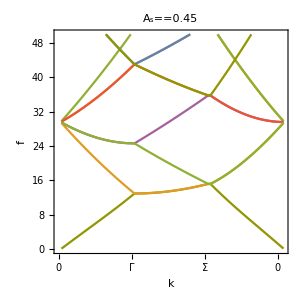

```mathematica
ListPlot[Reverse[Transpose[Join[vals4flathex,vals5flathex,vals6flathex]]],PlotLabel->Subscript[A,s]==hs,Joined->True,PlotRange->{0,50},Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameTicks->{{Automatic,Automatic},{{{0,0},{num,"Γ"},{2*num,"Σ"},{3*num,0}},{{0,""},{num,""},{2*num,""},{3*num,""}}}},ImageSize->300,AspectRatio->1,ImagePadding->{{65,15},{65,15}}]
```